```mathematica
f[μ_,η_]:=(16 μ (2+9 Sqrt[μ]+20 μ+27 μ^(3/2)+10 μ^2+23 μ^(5/2)+16 μ^3+5 μ^(7/2)))/((1+Sqrt[μ])^2 (1-Sqrt[μ]+3 μ+μ^(3/2)+4 μ^2)^2)
```

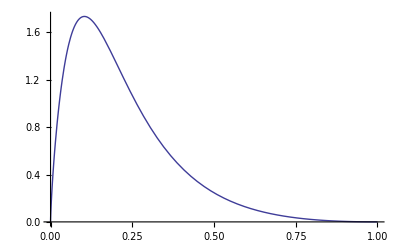

```mathematica
Clear[μ,η];
η=0;
Plot[f[μ,η]*Log[μ]^2/4/5,{μ,0,1}]
```

```mathematica
Clear[μ,η];
g[μ_,η_]:=(12 η (3 η^2+μ+4 η μ+4 η^3 μ+η^4 μ+3 η^2 μ^2))/((1+η)^2 (1-η+η^2+3 η μ)^2)
```

4.2

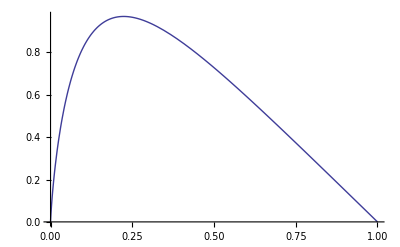

```mathematica
g[0.5,1]
Plot[-g[μ,1]/2*Log[μ]*μ,{μ,0,1}]
```

```mathematica
IE[μ_]:=(64 μ (1+22 μ+157 μ^2+692 μ^3+1697 μ^4+3382 μ^5+4467 μ^6+3360 μ^7+1582 μ^8))/(1+4 μ+22 μ^2+60 μ^3+113 μ^4+56 μ^5)^2;
```

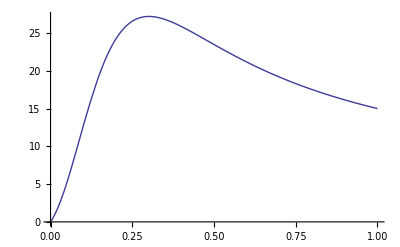

```mathematica
Clear[μ];
Plot[IE[μ],{μ,0,1}]
```

```mathematica
Clear[μ,η];
X[μ_,η_]:=(12 η (3 η^2+μ+4 η μ+4 η^3 μ+η^4 μ+3 η^2 μ^2))/((1+η)^2 (1-η+η^2+3 η μ)^2);
```

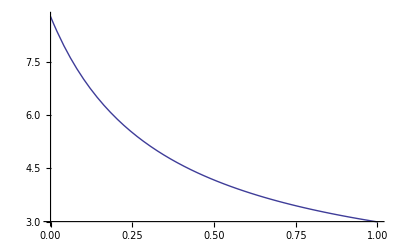

```mathematica
Plot[X[μ,0.9],{μ,0,1}]
```

```mathematica
Clear[μ,η];
Xx[μ_,η_]:=Log[μ]*μ*(4 η (81 η^8+4 μ+256 η^7 μ+256 η^9 μ+4 η^16 μ+4 μ^2+48 η μ^2+36 η^2 μ^2+32 η^3 μ^2+50 η^4 μ^2+144 η^5 μ^2+588 η^6 μ^2+256 η^7 μ^2+784 η^8 μ^2+256 η^9 μ^2+588 η^10 μ^2+144 η^11 μ^2+50 η^12 μ^2+32 η^13 μ^2+36 η^14 μ^2+48 η^15 μ^2+4 η^16 μ^2+μ^3+60 η μ^3+273 η^2 μ^3+368 η^3 μ^3+547 η^4 μ^3+1028 η^5 μ^3+1135 η^6 μ^3+1792 η^7 μ^3+1568 η^8 μ^3+1792 η^9 μ^3+1135 η^10 μ^3+1028 η^11 μ^3+547 η^12 μ^3+368 η^13 μ^3+273 η^14 μ^3+60 η^15 μ^3+η^16 μ^3+36 η μ^4+495 η^2 μ^4+1440 η^3 μ^4+2329 η^4 μ^4+2988 η^5 μ^4+3565 η^6 μ^4+4688 η^7 μ^4+4924 η^8 μ^4+4688 η^9 μ^4+3565 η^10 μ^4+2988 η^11 μ^4+2329 η^12 μ^4+1440 η^13 μ^4+495 η^14 μ^4+36 η^15 μ^4+216 η^2 μ^5+1808 η^3 μ^5+4358 η^4 μ^5+6616 η^5 μ^5+9348 η^6 μ^5+10152 η^7 μ^5+11268 η^8 μ^5+10152 η^9 μ^5+9348 η^10 μ^5+6616 η^11 μ^5+4358 η^12 μ^5+1808 η^13 μ^5+216 η^14 μ^5+51 η^2 μ^6+980 η^3 μ^6+4878 η^4 μ^6+11164 η^5 μ^6+16245 η^6 μ^6+19888 η^7 μ^6+20400 η^8 μ^6+19888 η^9 μ^6+16245 η^10 μ^6+11164 η^11 μ^6+4878 η^12 μ^6+980 η^13 μ^6+51 η^14 μ^6+9 η^2 μ^7+364 η^3 μ^7+3147 η^4 μ^7+10248 η^5 μ^7+19343 η^6 μ^7+26716 η^7 μ^7+29458 η^8 μ^7+26716 η^9 μ^7+19343 η^10 μ^7+10248 η^11 μ^7+3147 η^12 μ^7+364 η^13 μ^7+9 η^14 μ^7+48 η^3 μ^8+963 η^4 μ^8+5540 η^5 μ^8+15132 η^6 μ^8+24876 η^7 μ^8+29459 η^8 μ^8+24876 η^9 μ^8+15132 η^10 μ^8+5540 η^11 μ^8+963 η^12 μ^8+48 η^13 μ^8+108 η^4 μ^9+1584 η^5 μ^9+6188 η^6 μ^9+12224 η^7 μ^9+14656 η^8 μ^9+12224 η^9 μ^9+6188 η^10 μ^9+1584 η^11 μ^9+108 η^12 μ^9+528 η^6 μ^10+2112 η^7 μ^10+3232 η^8 μ^10+2112 η^9 μ^10+528 η^10 μ^10))/((1+η)^2 (1-η+η^2-η^3+η^4-η^5+η^6-η^7+η^8+4 η μ-4 η^2 μ+4 η^3 μ-4 η^4 μ+4 η^5 μ-4 η^6 μ+4 η^7 μ+4 η μ^2+8 η^2 μ^2-4 η^3 μ^2+6 η^4 μ^2-4 η^5 μ^2+8 η^6 μ^2+4 η^7 μ^2+η μ^3+14 η^2 μ^3+11 η^3 μ^3+8 η^4 μ^3+11 η^5 μ^3+14 η^6 μ^3+η^7 μ^3+9 η^2 μ^4+34 η^3 μ^4+27 η^4 μ^4+34 η^5 μ^4+9 η^6 μ^4+12 η^3 μ^5+32 η^4 μ^5+12 η^5 μ^5)^2);
```

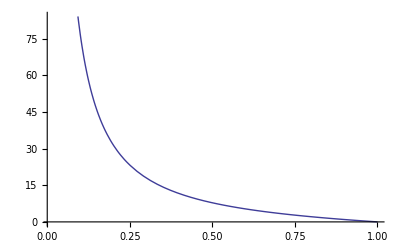

```mathematica
Plot[Xx[1/μ,1.0],{μ,0.01,1},]
```